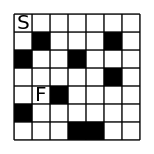

```mathematica
size=7;Style[Show[{pic[{{1,2},{1,5},{2,6},{3,3},{4,1},{4,5},{5,1},{6,4},{6,6}}],Graphics[{
Text[Style["S",FontSize->20],{1,7}-{.5,.55}],Text[Style["F",FontSize->20],{2,3}-{.5,.55}]}]},ImageSize->22size],Antialiasing->False]
```

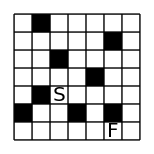

```mathematica
size=7;Style[Show[{pic[{{1,2},{2,3},{2,7},{3,5},{4,2},{5,4},{6,2},{6,6}}],Graphics[{
Text[Style["S",FontSize->20],{3,3}-{.5,.55}],Text[Style["F",FontSize->20],{6,1}-{.5,.55}]}]},ImageSize->22size],Antialiasing->False]
```

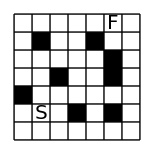

```mathematica
size=7;Style[Show[{pic[{{1,3},{2,6},{3,4},{4,2},{5,6},{6,2},{6,4},{6,5}}],Graphics[{
Text[Style["S",FontSize->20],{2,2}-{.5,.55}],Text[Style["F",FontSize->20],{6,7}-{.5,.55}]}]},ImageSize->22size],Antialiasing->False]
```

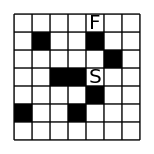

```mathematica
size=7;Style[Show[{pic[{{1,2},{2,6},{3,4},{4,2},{4,4},{5,3},{5,6},{6,5}}],Graphics[{
Text[Style["S",FontSize->20],{5,4}-{.5,.55}],Text[Style["F",FontSize->20],{5,7}-{.5,.55}]}]},ImageSize->22size],Antialiasing->False]
```

```mathematica
size=6;Style[Show[{pic[{{1,5},{2,1},{3,1},{2,5},{3,3},{5,4},{6,2}}],Graphics[{
Text[Style["S",FontSize->20],{1,2}-{.5,.55}],Text[Style["F",FontSize->20],{2,6}-{.5,.55}]}]},ImageSize->22size],Antialiasing->False]
```

-Graphics-

```mathematica
size=6;Style[Show[{pic[{{1,5},{2,1},{4,3},{3,4},{5,5},{6,4}}],Graphics[{
Text[Style["S",FontSize->20],{4,1}-{.5,.55}],Text[Style["F",FontSize->20],{6,3}-{.5,.55}]}]},ImageSize->22size],Antialiasing->False]
```

-Graphics-

```mathematica
size=5;Style[Show[{pic[{{2,2},{2,3},{5,1},{5,5},{4,4}}],Graphics[{
Text[Style["S",FontSize->20],{1,3}-{.5,.55}],Text[Style["F",FontSize->20],{1,2}-{.5,.55}]}]},ImageSize->22size],Antialiasing->False]
```

-Graphics-

```mathematica
size=5;Style[Show[{pic[{{1,3},{3,2},{3,3},{5,4}}],Graphics[{Text[Style["S",FontSize->20],{2,2}-{.5,.55}],Text[Style["F",FontSize->20],{4,2}-{.5,.55}]}]},ImageSize->110],Antialiasing->False]
```

-Graphics-

```mathematica
Style[Graphics[{
Table[Line[{{0,i},{4,i}}],{i,1,4}],
Table[Line[{{i,1},{i,4}}],{i,0,4}],
Text[Style["S",FontSize->20],{3.5,2.45}],Text[Style["F",FontSize->20],{2.5,2.45}],
Hue[0,1/3],
Rectangle[{3.35,3.35},{3.65,3.65}],Rectangle[{2.35,3.35},{2.65,3.65}],Rectangle[{.8,3.35},{1.2,3.65}],Rectangle[{1.8,3.35},{2.2,3.65}],Rectangle[{1.8,2.35},{2.2,2.65}],Rectangle[{.8,2.35},{1.2,2.65}],Rectangle[{3.35,1.8},{3.65,2.2}],Rectangle[{2.35,1.8},{2.65,2.2}],Black,Text[8,{1,2.5}],Text[7,{1,3.5}],Text[6,{2.5,3.5}],Text[5,{2.5,2}],Text[4,{3.5,2}],Text[3,{3.5,3.5}],Text[2,{2,3.5}],Text[1,{2,2.5}],Rectangle[{1,1},{2,2}]
},ImageSize->120],Antialiasing->False]
```

-Graphics-

```mathematica
p[{x_,y_}]:=A[[x,y]]
pic[L_]:=Graphics[{
Table[Line[{{0,i},{size,i}}],{i,0,size}],
Table[Line[{{i,0},{i,size}}],{i,0,size}],
Map[Rectangle[#,#-1]&,L]
},ImageSize->100]
```

```mathematica
f[L_]:=Module[{},
A=ReplacePart[Table[0,{size},{size}],L->1];
A=Transpose[Table[1,{2},{Length[A[[1]]]}]~Join~A~Join~Table[1,{2},{Length[A[[1]]]}]];
A=Transpose[Table[1,{2},{Length[A[[1]]]}]~Join~A~Join~Table[1,{2},{Length[A[[1]]]}]];

edges={};
stack={{{3,3},3}};
positions={stack[[1]]};
While[Length[stack]>0,
top=stack[[1]];
stack=Rest[stack];
state=Last[top];
pos=First[top];

If[state==1&&p[pos+{0,2}]==0,
t={pos+{0,2},3};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];
If[state==1&&p[pos+{0,-1}]==0,
t={pos+{0,-1},3};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];
If[state==1&&p[pos+{-1,0}]==0&&p[pos+{-1,1}]==0,
t={pos+{-1,0},1};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];If[state==1&&p[pos+{1,0}]==0&&p[pos+{1,1}]==0,
t={pos+{1,0},1};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];

If[state==2&&p[pos+{2,0}]==0,
t={pos+{2,0},3};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];
If[state==2&&p[pos+{-1,0}]==0,
t={pos+{-1,0},3};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];
If[state==2&&p[pos+{0,1}]==0&&p[pos+{1,1}]==0,
t={pos+{0,1},2};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];If[state==2&&p[pos+{0,-1}]==0&&p[pos+{1,-1}]==0,
t={pos+{0,-1},2};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];

If[state==3&&p[pos+{0,-1}]==0&&p[pos+{0,-2}]==0,
t={pos+{0,-2},1};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];
If[state==3&&p[pos+{0,1}]==0&&p[pos+{0,2}]==0,
t={pos+{0,1},1};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];
If[state==3&&p[pos+{-1,0}]==0&&p[pos+{-2,0}]==0,
t={pos+{-2,0},2};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];If[state==3&&p[pos+{1,0}]==0&&p[pos+{2,0}]==0,
t={pos+{1,0},2};
If[Not[MemberQ[positions,t]],AppendTo[stack,t];AppendTo[edges,top->t]]];

positions=Union[positions~Join~{top}]];
GraphPlot[edges,MultiedgeStyle->False,ImageSize->{600,300}]]
```

```mathematica
diameter:=Module[{},
vertices=Union[Flatten[Map[{#[[1]],#[[2]]}&,edges],1]];B=Table[0,{Length[vertices]},{Length[vertices]}];
For[i=1,i≤Length[edges],i++,
a=edges[[i,1]];
b=edges[[i,2]];
pa=Position[vertices,a][[1,1]];
pb=Position[vertices,b][[1,1]];
B=ReplacePart[B,{{pa,pb},{pb,pa}}->1]];
Clear[P];
P[1]=B;
P[i_]:=P[i]=Map[Sign,B.P[i-1]+P[i-1],2];
For[i=minsize,i≤Length[vertices+1],i++,
If[Union[Flatten[P[i]-P[i-1]]]=={0},Return[i-1];Break[]]]]
```

```mathematica
all[L_]:=(f[L];d=diameter;Print[pic[L]];Print[d];Print[f[L]])
```

## generation

-Graphics-

45

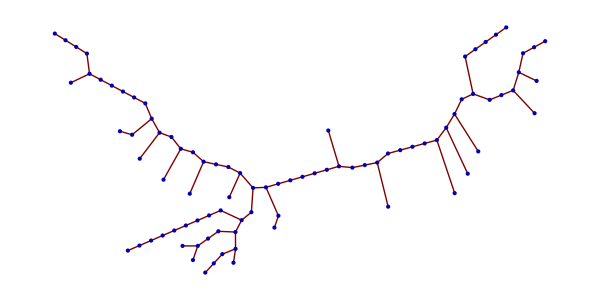

-Graphics-

40

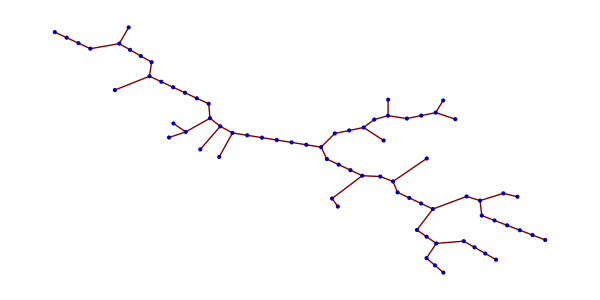

-Graphics-

44

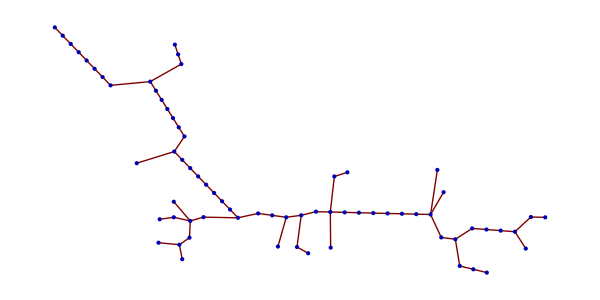

-Graphics-

43

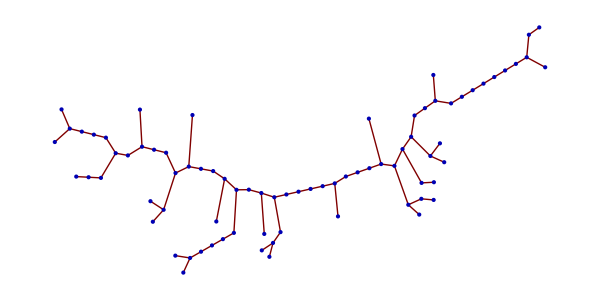

-Graphics-

42

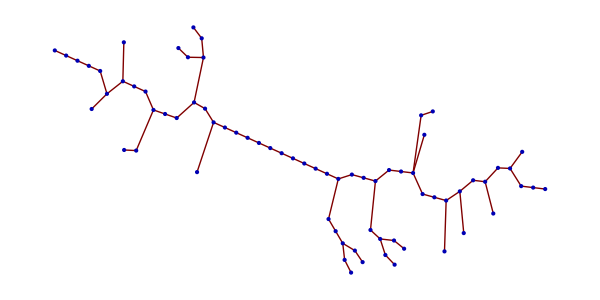

-Graphics-

42

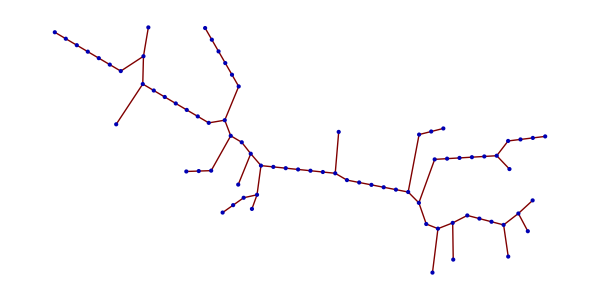

-Graphics-

41

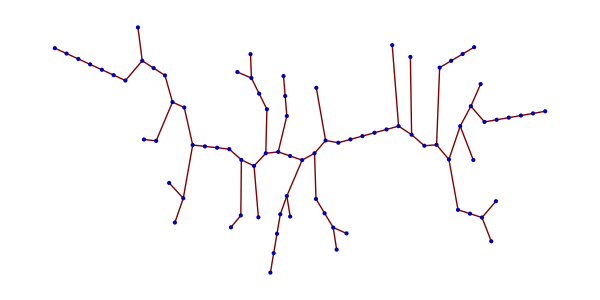

```mathematica
size=7;
minsize=40;
For[m=1,m>0,m++,
L={};
blocks=RandomInteger[{6,10}];
While[Length[L]<blocks,
a=RandomInteger[{1,size}];b=RandomInteger[{1,size}];
While[a<2&&b<2,a=RandomInteger[{1,size}];b=RandomInteger[{1,size}]];
L=Union[L~Join~{{a,b}}]];
f[L];d=diameter;
If[d≥minsize,Print[pic[L]];Print[d];Print[f[L]]]]
```

## 6x6

-Graphics-

31

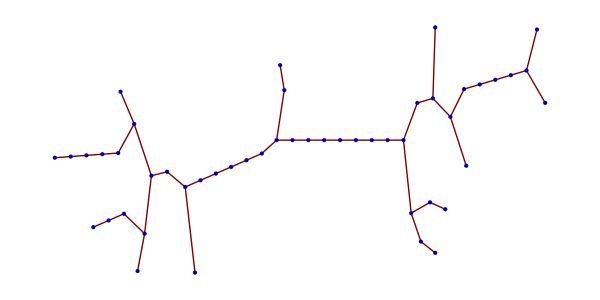

-Graphics-

33

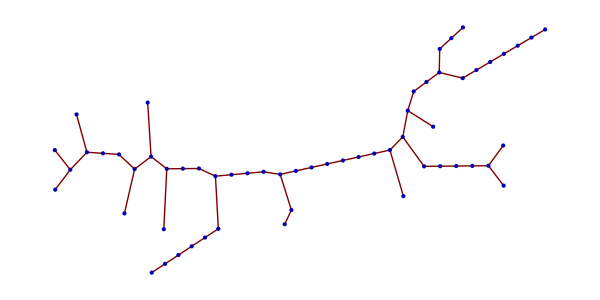

-Graphics-

30

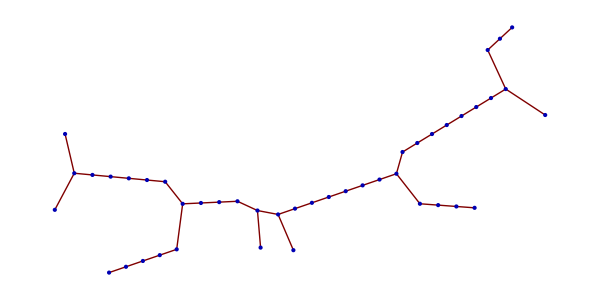

-Graphics-

32

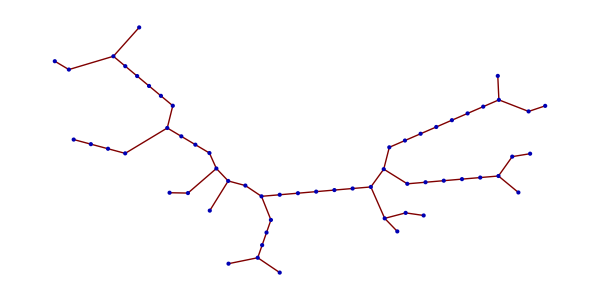

-Graphics-

33

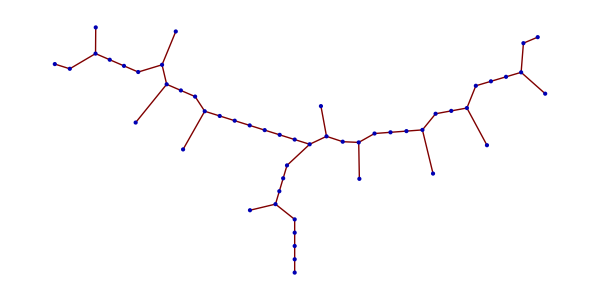

-Graphics-

34

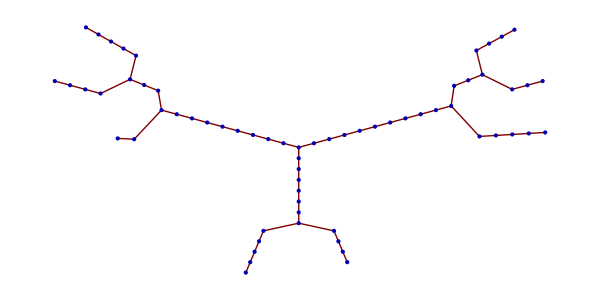

-Graphics-

30

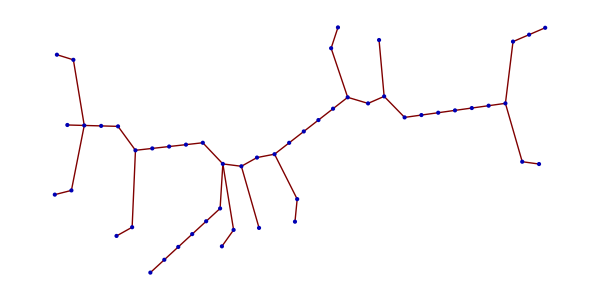

## 7x7

-Graphics-

47

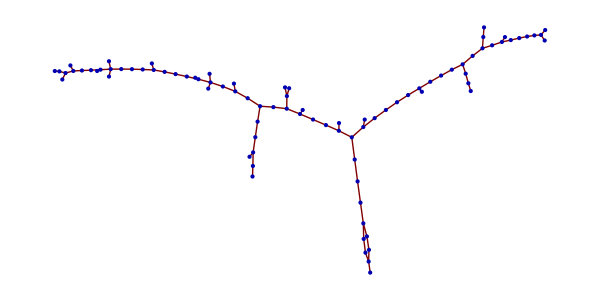

-Graphics-

42

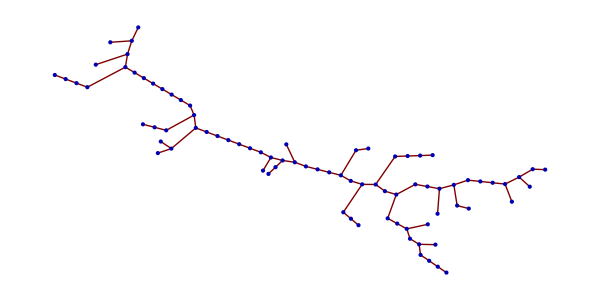

-Graphics-

47